# Curved shell

This notebook presents ray tracing/quantization results for a shell that’s curved along the x axis.

```mathematica
$Assumptions = _ ∈ Reals;
```

## Ray analysis

```mathematica
H=({{k^4+2 k^2 l^2+l^4+m^2, -ⅈ k m, -ⅈ l η m}, {ⅈ k m, k^2+1/2 l^2 (1-η), 1/2 k l (1+η)}, {ⅈ l η m, 1/2 k l (1+η), l^2+1/2 k^2 (1-η)}});
```

Verify that our expression Λ for the determinant is correct.

```mathematica
Λ=m^2((ω^2-1/2(1-η)l^2)(ω^2-(1-η^2)l^2)-1/2(1-η)k^2 ω^2)-(ω^2-(k^2+l^2)^2)(ω^2-(k^2+l^2))(ω^2-1/2(1-η)(k^2+l^2));
Det[H-ω^2 IdentityMatrix[{3,3}]]-Λ//Simplify
```

0

## Quantization

```mathematica
(*  Finds a quantized orbit near another (approximately quantized) 
		orbit by minimizing the estimated quantum number.  *)
quantize[m_, dm_, mInv_, ωGuess_?NumericQ, ϵ_?NumericQ, l:(_?NumericQ):0.1, η:(_?NumericQ):0.3, δ:(_?NumericQ):0.01, OptionsPattern[]] := Module[
	{t, x, k, eqs, sol, caustic, actionIntegral, nEst, ωEst, n, ωRandGuess, res, S},
	
	(*  Location of the caustic on the negative x axis.  *)
	caustic[ω_]:= -mInv[√((ω^2-l^2)/(ω^2-(1-η^2)l^2)(ω^2-l^4))];
	
	(* For reasons I don't care for, we need to integrate the shear rays 
		 backwards to get positive quantum numbers n. *)
	If[OptionValue["Backwards"], S = -1, S = 1];
	
	actionIntegral[ω_] := (
		(*  Set up all equations.  *)
		eqs = {
			x'[t] == S(k[t] (-4 (-1+η) (l^2+k[t]^2)^3+ω^4 (3+4 l^2-η+4 k[t]^2)+ω^2 (l^2+k[t]^2) (3 l^2 (-3+η)+2 (-1+η)+3 (-3+η) k[t]^2)+(-1+η) ω^2 m[x[t]]^2)), 
			k'[t] == -S(((l^2 (-1+η^2)+ω^2) (l^2 (-1+η)+2 ω^2)+(-1+η) ω^2 k[t]^2) m[x[t]] dm[x[t]]),
			k[0] == 0,
			x[0] == caustic[ω],
			
			(*  Ensure that we stop the integration once we reach the turning 
					point on the positive x axis.  We will always start the integration 
					from the turning point on the negative x axis.  *)
			WhenEvent[k[t] == 0 && t > 0, "StopIntegration"]
		};
		
		(*  We should ideally be using a sympletic integrator.  *)
		sol = NDSolve[eqs, {x, k}, {t, 0, ∞}];
		
		(*  Use the undocumented "Domain" method of InterpolatingFunction
				to get the the time at which we hit the next turning point.  *)
		NIntegrate[k[t]D[x[t], t]/.First@sol, {t}~Join~(First@(x/.First@sol)["Domain"])]
	);
	
	(*  Roughly estimate the quantum number n.  *)
	nEst[ωEst_?NumericQ] := actionIntegral[ωEst]/(ϵ π) - 0.5;
	n = Round[nEst[ωGuess]];
	
	If[OptionValue["RandMin"],
		ωRandGuess = RandomReal[{ωGuess - δ, ωGuess + δ}, OptionValue["NRand"]]~Join~{ωGuess};
		res = (nEst[#] - n)^2 & /@ ωRandGuess;
		ωRandGuess = ωRandGuess[[Ordering[res, 1]]][[1]];
		{Round[nEst[ωRandGuess]], ωRandGuess, Min[res]},
		res = ωEst/.FindRoot[nEst[ωEst] - n, {ωEst, ωGuess}];
		{n, res, Abs[(nEst[res] - n)]/(n + 10^-1)}
	]
];

Options[quantize] = {"RandMin"->False, "NRand"->10, "Backwards"->False};
```

### sech type

```mathematica
m[x_]:=0.1-(0.1-0.01)Sech[x];
dm[x_]:=(0.1-0.01)Sech[x]Tanh[x];
mInv[ω_?NumericQ]:=-ArcSech[(0.1-ω)/(0.1-0.01)];
```

```mathematica
ωSpectral1 = (Transpose@Import["~/code/glwtes/shell/data/sech_bc_cc_l_0.1_eps_0.01_b0.1_a0.01_N_2048/quantized1.txt","Table"])[[1]];
ωQuantized1 = ParallelMap[quantize[m, dm, mInv,#, 0.01,"Backwards"->False]&,ωSpectral1];
Export["~/code/glwtes/shell/data/sech_bc_cc_l_0.1_eps_0.01_b0.1_a0.01_N_2048/wkb1.txt",ωQuantized1,"Table"];
```

```mathematica
ωSpectral2 = (Transpose@Import["~/code/glwtes/shell/data/sech_bc_cc_l_0.1_eps_0.01_b0.1_a0.01_N_2048/quantized2.txt","Table"])[[1]];
ωQuantized2 = ParallelMap[quantize[m, dm, mInv,#, 0.01,"Backwards"->True]&,ωSpectral2];
Export["~/code/glwtes/shell/data/sech_bc_cc_l_0.1_eps_0.01_b0.1_a0.01_N_2048/wkb2.txt",ωQuantized1,"Table"];
```

```mathematica
ωSpectral3 = (Transpose@Import["~/code/glwtes/shell/data/sech_bc_cc_l_0.1_eps_0.01_b0.1_a0.01_N_2048/quantized3.txt","Table"])[[1]];
ωQuantized3 = ParallelMap[quantize[m, dm, mInv,#, 0.01,"Backwards"->False]&,ωSpectral3];
Export["~/code/glwtes/shell/data/sech_bc_cc_l_0.1_eps_0.01_b0.1_a0.01_N_2048/wkb3.txt",ωQuantized3,"Table"];
```

### tanh type

```mathematica
m[x_]:=0.1Tanh[x];
dm[x_]:=0.1 Sech[x]^2;
mInv[ω_?NumericQ]:=-ArcTanh[10ω];
```

```mathematica
ωSpectral1 = (Transpose@Import["~/code/glwtes/shell/data/tanh_bc_cc_l_0.1_eps_0.01_b0.1_N_2048/quantized1.txt","Table"])[[1]];
ωQuantized1 = ParallelMap[quantize[m, dm, mInv,#, 0.01,"Backwards"->False]&,ωSpectral1];
Export["~/code/glwtes/shell/data/tanh_bc_cc_l_0.1_eps_0.01_b0.1_N_2048/wkb1.txt",ωQuantized1,"Table"];
```

```mathematica
ωSpectral2 = (Transpose@Import["~/code/glwtes/shell/data/tanh_bc_cc_l_0.1_eps_0.01_b0.1_N_2048/quantized2.txt","Table"])[[1]];
ωQuantized2 = ParallelMap[quantize[m, dm, mInv,#, 0.01,"Backwards"->True]&,ωSpectral2];
Export["~/code/glwtes/shell/data/tanh_bc_cc_l_0.1_eps_0.01_b0.1_N_2048/wkb2.txt",ωQuantized2,"Table"];
```

```mathematica
ωSpectral3 = (Transpose@Import["~/code/glwtes/shell/data/tanh_bc_cc_l_0.1_eps_0.01_b0.1_N_2048/quantized3.txt","Table"])[[1]];
ωQuantized3 = ParallelMap[quantize[m, dm, mInv,#, 0.01,"Backwards"->False]&,ωSpectral3];
Export["~/code/glwtes/shell/data/tanh_bc_cc_l_0.1_eps_0.01_b0.1_N_2048/wkb3.txt",ωQuantized3,"Table"];
```

#### altsech type

```mathematica
m[x_]:=0.1Sech[x];
dm[x_]:=-0.1Sech[x]Tanh[x];
mInv[ω_?NumericQ]:=-ArcSech[10ω];
```

```mathematica
ωSpectral = (Transpose@Import["~/code/glwtes/shell/data/altsech_bc_cc_l_0.1_eps_0.01_b0.1_N_512/quantized.txt","Table"])[[1]];
ωQuantized = ParallelMap[quantize[m, dm, mInv,#, 0.01,"Backwards"->True]&,ωSpectral];Export["~/code/glwtes/shell/data/altsech_bc_cc_l_0.1_eps_0.01_b0.1_N_512/wkb.txt",ωQuantized,"Table"];
```

## Dispersion curves

```mathematica
dispersion[k_,l_,η_,m_]:=Block[{Λ,ω},
Λ=-((-k^2-l^2+ω^2) (-(k^2+l^2)^2+ω^2) (-1/2 (k^2+l^2) (1-η)+ω^2))+m^2 (-1/2 k^2 (1-η) ω^2+(-1/2 l^2 (1-η)+ω^2) (-l^2 (1-η^2)+ω^2));
Select[ω/.Solve[Λ==0,ω], (# > 0)&]
]
```

General cubic solution:

```mathematica
Clear[a,b,c,d];
sol={a/3+(2^(1/3) (a^2+3 b))/(3 d)+d/(3 2^(1/3)),a/3-((1-ⅈ √3) (a^2+3 b))/(3 2^(2/3) d)-((1+ⅈ √3) d)/(6 2^(1/3)),a/3-((1+ⅈ √3) (a^2+3 b))/(3 2^(2/3) d)-((1-ⅈ √3) d)/(6 2^(1/3))};
d=(2 a^3+9 a b+27 c+3 √3 √(-a^2 b^2-4 b^3+4 a^3 c+18 a b c+27 c^2))^(1/3);
```

Find the coefficients a,b,c and check if have everything right:

```mathematica
{c,b,a}=(CoefficientList[Λ,ω^2]/.{k->√(q^2-l^2)}//FullSimplify)[[1;;3]]
Λ+(ω^6-a ω^4-b ω^2-c)/.{k->√(q^2-l^2)}//FullSimplify
sol=sol/.{q->√(k^2+l^2)};
```

{1/2 (-1+η) (-q^8+l^4 m^2 (-1+η^2)),1/2 (m^2 q^2 (-1+η)+q^4 (-1+q^2 (-3+η)+η)+2 l^2 m^2 (-1+η^2)),m^2+1/2 q^2 (3+2 q^2-η)}

0

### Extensional

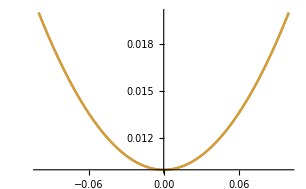

```mathematica
Plot[{k^2+0.1^2,sol[[1]]/.{l->0.1,m->0,η->0.3}},{k,-0.1,0.1},PlotPoints->100]
```

### Shear

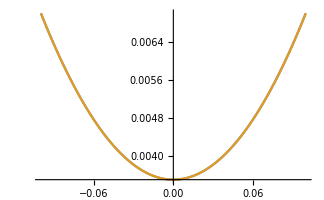

```mathematica
Plot[{1/2(1-0.3)(k^2+0.1^2),sol[[2]]/.{l->0.1,m->0,η->0.3}},{k,-0.1,0.1},PlotPoints->100]
```

### Flexural

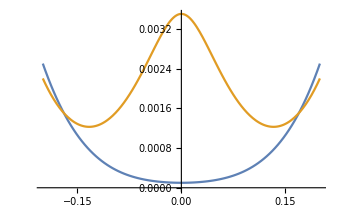

```mathematica
Plot[{(k^2+0.1^2)^2,sol[[3]]/.{l->0.1,m->0.1,η->0.3}},{k,-0.2,0.2},PlotPoints->100]
```

### Double well minima in flexural dispersion

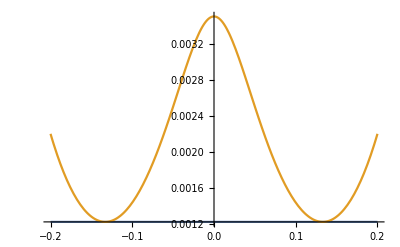

```mathematica
Plot[{0.03502325^2,sol[[3]]/.{l->0.1,m->0.1,η->0.3}},{k,-0.2,0.2},PlotPoints->100]
```

## Phase portraits (curvature profile with minimum)

### Flexural

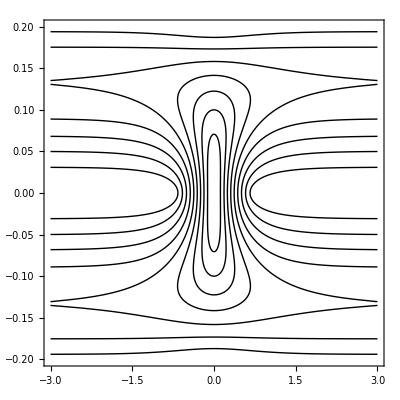

```mathematica
ContourPlot[√sol[[3]]/.{l->0.1,m->0.1Tanh[x],η->0.3},{x,-3,3},{k,-0.2,0.2},ContourShading->None,PlotPoints->100]
```

### Shear

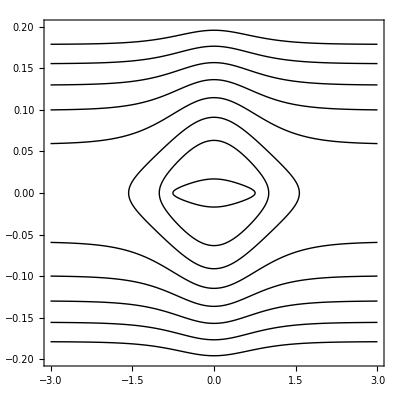

```mathematica
ContourPlot[√sol[[2]]/.{l->0.1,m->0.1Tanh[x],η->0.3},{x,-3,3},{k,-0.2,0.2},ContourShading->None,PlotPoints->100]
```

### Extensional

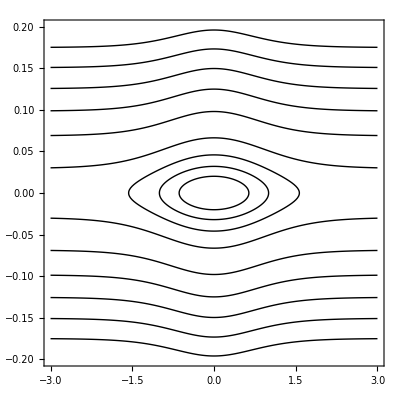

```mathematica
ContourPlot[√sol[[1]]/.{l->0.1,m->0.1Tanh[x],η->0.3},{x,-3,3},{k,-0.2,0.2},ContourShading->None,PlotPoints->100,Contours->{0.102,0.105,0.11}~Join~Range[0.12,0.22,0.02]]
```

Can shear waves localize when the curvature is small?  Yes, e.g., with max curvature = 0.01, shear wave cut on at l=0.01 is 0.00591608. Max localization frequency is 0.0083669.

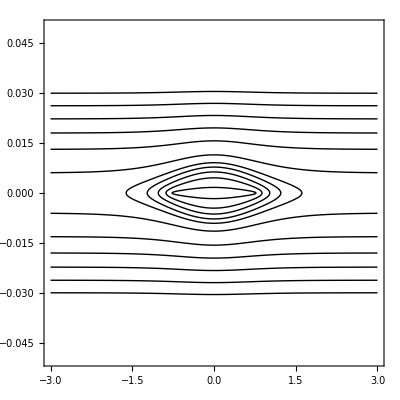

```mathematica
ContourPlot[√sol[[2]]/.{l->0.01,m->0.01Tanh[x],η->0.3},{x,-3,3},{k,-0.05,0.05},ContourShading->None,PlotPoints->100,Contours->Range[0.006,0.008,0.0005]~Join~Range[0.009,0.02,0.002]]
```

## Phase portraits (curvature profile with maximum)

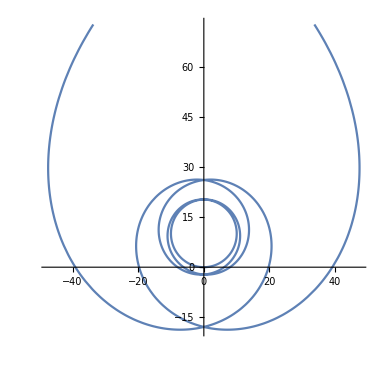

```mathematica
β[x_,ϵ_,b_]:=(2 b ArcTan[Tanh[(x ϵ)/2]])/ϵ;
R[x_,ϵ_,b_]:=NIntegrate[{Cos[β[t,ϵ,b]],Sin[β[t,ϵ,b]]},{t,0,x}]
ParametricPlot[R[x,0.01,0.1],{x,-300,300},PlotRange->Full]
```

### Flexural

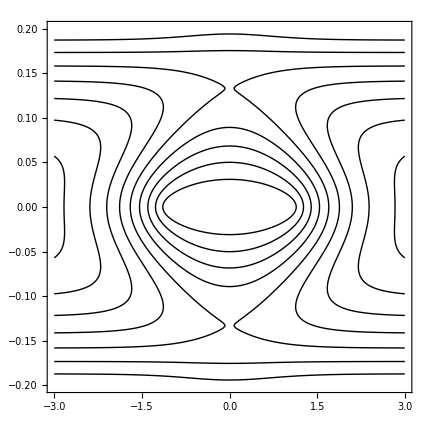

```mathematica
ContourPlot[√sol[[3]]/.{l->0.1,m->0.1Sech[x],η->0.3},{x,-3,3},{k,-0.2,0.2},ContourShading->None,PlotPoints->100]
```

For b < m_dagger , the orbits are not flattened like they are for b>m_dagger.

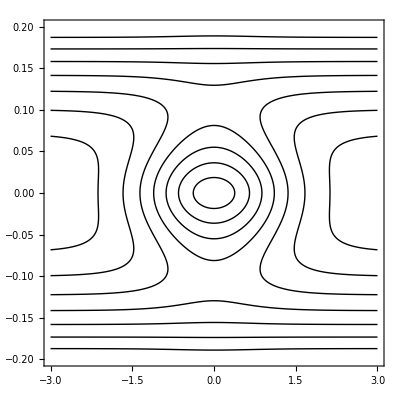

```mathematica
ContourPlot[√sol[[3]]/.{l->0.1,m->0.05Sech[x],η->0.3},{x,-3,3},{k,-0.2,0.2},ContourShading->None,PlotPoints->100]
```

Bound states disappear when l=0.

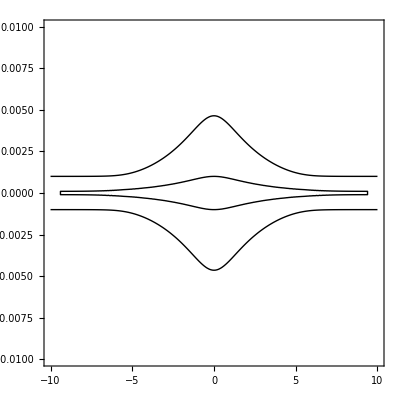

```mathematica
ContourPlot[Re[√sol[[3]]/.{l->0,m->0.1Sech[x],η->0.3}],{x,-10,10},{k,-0.01,0.01},ContourShading->None,Contours->{10^-8,10^-6,10^-4}~Join~Range[0.0001,0.001,0.0005],PlotPoints->100]
```

### Extensional

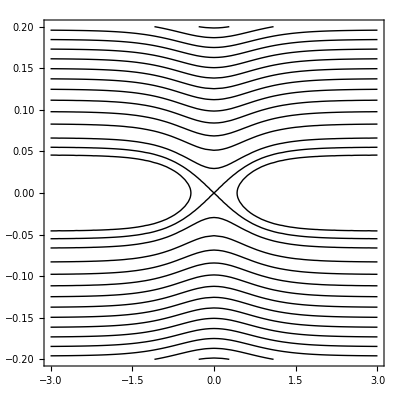

```mathematica
ContourPlot[√sol[[1]]/.{l->0.1,m->0.1Sech[x],η->0.3},{x,-3,3},{k,-0.2,0.2},ContourShading->None,PlotPoints->20,Contours->{0.11423842014723197}~Join~Range[0.0,0.3,0.01]]
```

### Shear

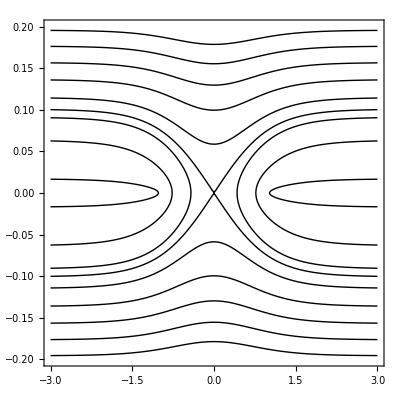

```mathematica
ContourPlot[√sol[[2]]/.{l->0.1,m->0.1Sech[x],η->0.3},{x,-3,3},{k,-0.2,0.2},ContourShading->None,PlotPoints->100,Contours->{0.08396179704046661}~Join~Range[0.0,0.3,0.01]]
```

## Additional phases (general version)

Dispersion matrix is

```mathematica
D0=({{Z0-ω^2, ⅈ A0, ⅈ B0}, {-ⅈ A0, U0-ω^2, C0}, {-ⅈ B0, C0, V0-ω^2}});
```

First-order correction to the dispersion matrix:

```mathematica
D1=({{0, A1, B1}, {A1, 0, ⅈ C1}, {B1, -ⅈ C1, 0}});
```

Polarization τ=(r Exp[I ϕ], τ_1,τ_2) is

```mathematica
τ={r Exp[I ϕ],Subscript[τ, 2],Subscript[τ, 3]}/.Solve[(D0.{r Exp[I ϕ],Subscript[τ, 2],Subscript[τ, 3]})[[2;;3]]==0,{Subscript[τ, 2],Subscript[τ, 3]}][[1]];
```

Rephasing τ with Exp(-i ϕ) we arrive at

```mathematica
Exp[-I ϕ]τ//Simplify
```

{r,(ⅈ r (B0 C0+A0 (-V0+ω^2)))/(C0^2+(U0-ω^2) (-V0+ω^2)),(ⅈ r (A0 C0+B0 (-U0+ω^2)))/(C0^2+(U0-ω^2) (-V0+ω^2))}

so that

```mathematica
τ={x,I y,I z};
```

The 2nd term in the non-geometric phase is:

```mathematica
τ†.(D1.τ)//Simplify
```

0